```mathematica
Clear [x,t,a,ω,l];
```

```mathematica
weqn=D[u[x,t],{t,2}]==a^2 D[u[x,t],{x,2}];
```

```mathematica
ic={u[x,0]==0,Derivative[0,1][u][x,0]==(-Sin[ω x/a])/Sin[(ω l)/a]};
```

```mathematica
bc={u[0,t]==0,u[l,t]==0};
```

```mathematica
sol=DSolve[{weqn,bc,ic},u[x,t],{x,t}]/.{K[1]->m}
```

{{u[x,t]→(2 (-1)^m √(a^2) l Sin[(√(a^2) m π t)/l] Sin[(m π x)/l])/(a^2 m^2 π^2-l^2 ω^2)m1∞}}

```mathematica
asol[ω_,a_,l_,x_,t_]=u[x,t]/.sol[[1]]/.{∞->4}//Activate
```

-(2 √(a^2) l Sin[(√(a^2) π t)/l] Sin[(π x)/l])/(a^2 π^2-l^2 ω^2)+(2 √(a^2) l Sin[(2 √(a^2) π t)/l] Sin[(2 π x)/l])/(4 a^2 π^2-l^2 ω^2)-(2 √(a^2) l Sin[(3 √(a^2) π t)/l] Sin[(3 π x)/l])/(9 a^2 π^2-l^2 ω^2)+(2 √(a^2) l Sin[(4 √(a^2) π t)/l] Sin[(4 π x)/l])/(16 a^2 π^2-l^2 ω^2)

```mathematica
f[t_,ω_,a_,l_]:=Plot[asol[ω,a,l,x,t],{x,0,π},PlotRange->{-10,10}]
```

```mathematica
Manipulate[Plot[asol[ω,a,l,x,t],{x,0,2l},PlotRange->{-1,1}],{t,0,4Pi},{ω,0,20},{a,1,2},{l,π/2,2π},SaveDefinitions->True]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

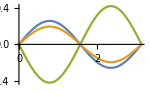
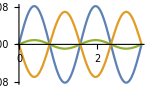
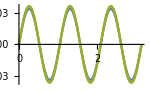
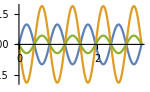

```mathematica
Table[Show[Plot[Table[asol[x,ω][[m]],{ω,1.9,3.9}]//Evaluate,{x,0,Pi},Ticks->False],ImageSize->150],{m,4}]
```